# Rossller System

The Rossller system is
	x' | = | -y-z
y' | = | x+a y
z' | = | b+z(x-c)
The std parameters are a=b=0.2 and c=5.7

```mathematica
Clear[Ross]
TMax=123;
Ross[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z,x+a y, b + z (x-c)}
{a,b,c}={0.2,0.2,5.7};
wSol= NDSolveValue[ {w'[t]==Ross[{a,b,c}][w[t]],w[0]=={1,2,3}},w,{t,0,TMax}];
ParametricPlot3D[wSol[t],{t,0, TMax},PlotPoints->100,PlotRange->All]
```

-Graphics3D-

Think about this as 
	y' | = | f(y) | with | y(0)=x
This defines a function of t and x say  y(t,x) which we can partial differentiate with respect to x!  
We can differentiate the ODE with respect to the vector of initial conditions x.   We are going to work through this slowly!
	∇_x y' | = | ∇_x (f(y)) | with | ∇_x y(0)=∇_x x.
If we interchange the order of differentiation, apply the chain rule and think about the initial conditions we get
	 (∇_x y)' | = | Df(y)∇_x (y) | with | ∇_x y(0)=Id.
All we have to do now is decide to call the Jacobian ∇_x y a reasonable name like J to get
	J' | = | Df(y)J | with | J(0)=Id.
This is an IVP for the sensitivity of the solution at any time t with respect to the initial condition x.

Shockingly it is called the “sensitivity equation”.

InterpolatingFunction[…]

-Graphics3D-

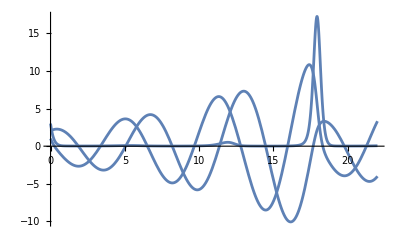

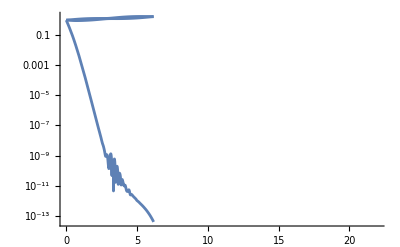

```mathematica
Clear[Ross]
TMax=22;
Ross[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z,x+a y, b + z (x-c)}
dRoss[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
{a,b,c}={0.2,0.2,5.7};
Id={{1,0,0},{0,1,0},{0,0,1}};
wSol= NDSolveValue[ {w'[t]==Ross[{a,b,c}][w[t]],w[0]=={1,2,3}},w,{t,0,TMax}];
JSol=NDSolveValue[ {J'[t]==dRoss[{a,b,c}][wSol[t]].J[t],J[0]==Id},J,{t,0,TMax}]
ParametricPlot3D[wSol[t],{t,0, TMax},PlotPoints->100,PlotRange->All]
Plot[wSol[t],{t,0, TMax},PlotPoints->100,PlotRange->All]
LogPlot[SingularValueList[JSol[t]],{t,0, TMax}]
```